```mathematica
SetDirectory["/home/jhofman/Desktop/SC/assignment4/Data/"];
Needs["PlotLegends`"]
```

## jacobi

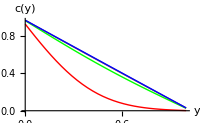

```mathematica
ListPlot[{Flatten[Drop[Import["data.32jac1e-03","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-04","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-05","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-06","Table"],None,-31]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue},AxesLabel->{"y","c(y)"},ImageSize->200]
```

```mathematica
ListPlot[{Flatten[Drop[Import["data.256jac1e-03","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-04","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-05","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-06","Table"],None,-255]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue},AxesLabel->{"y","c(y)"},ImageSize->200]
```

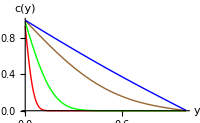

```mathematica
ListPlot[{Flatten[Drop[Import["data.1024jac1e-03","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-04","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-05","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-06","Table"],None,-1023]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue},PlotLegend->{"δ = 10^-3","δ = 10^-4","δ = 10^-5","δ = 10^-6"},AxesLabel->{"y","c(y)"},LegendShadow->None,ImageSize->200,PlotRange->All]
```

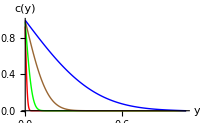

## Gauss

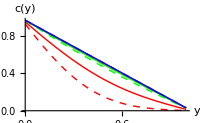

```mathematica
ListPlot[{Flatten[Drop[Import["data.32gauss1e-03","Table"],None,-31]],Flatten[Drop[Import["data.32gauss1e-04","Table"],None,-31]],Flatten[Drop[Import["data.32gauss1e-05","Table"],None,-31]],Flatten[Drop[Import["data.32gauss1e-06","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-03","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-04","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-05","Table"],None,-31]],Flatten[Drop[Import["data.32jac1e-06","Table"],None,-31]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue,{Red,Dashed},{Green,Dashed},{Brown,Dashed},{Blue,Dashed}},AxesLabel->{"y","c(y)"},ImageSize->200]
```

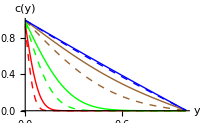

```mathematica
ListPlot[{Flatten[Drop[Import["data.256gauss1e-03","Table"],None,-255]],Flatten[Drop[Import["data.256gauss1e-04","Table"],None,-255]],Flatten[Drop[Import["data.256gauss1e-05","Table"],None,-255]],Flatten[Drop[Import["data.256gauss1e-06","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-03","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-04","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-05","Table"],None,-255]],Flatten[Drop[Import["data.256jac1e-06","Table"],None,-255]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue,{Red,Dashed},{Green,Dashed},{Brown,Dashed},{Blue,Dashed}},AxesLabel->{"y","c(y)"},ImageSize->200]
```

```mathematica
ListPlot[{Flatten[Drop[Import["data.1024gauss1e-03","Table"],None,-1023]],Flatten[Drop[Import["data.1024gauss1e-04","Table"],None,-1023]],Flatten[Drop[Import["data.1024gauss1e-05","Table"],None,-1023]],Flatten[Drop[Import["data.1024gauss1e-06","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-03","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-04","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-05","Table"],None,-1023]],Flatten[Drop[Import["data.1024jac1e-06","Table"],None,-1023]]},DataRange->{0,1},Joined->True,PlotStyle->{Red,Green,Brown,Blue,{Red,Dashed},{Green,Dashed},{Brown,Dashed},{Blue,Dashed}},PlotLegend->{"δ = 10^-3","δ = 10^-4","δ = 10^-5","δ = 10^-6","δ = 10^-3","δ = 10^-4","δ = 10^-5","δ = 10^-6"},AxesLabel->{"y","c(y)"},LegendShadow->None,ImageSize->200,PlotRange->All]
```

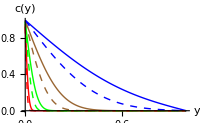

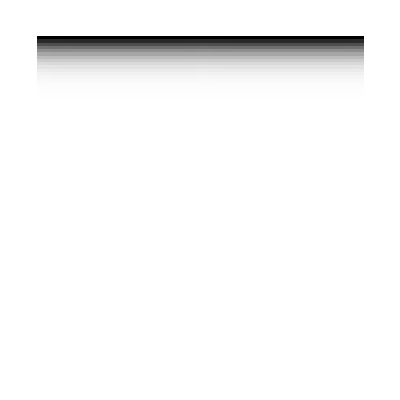

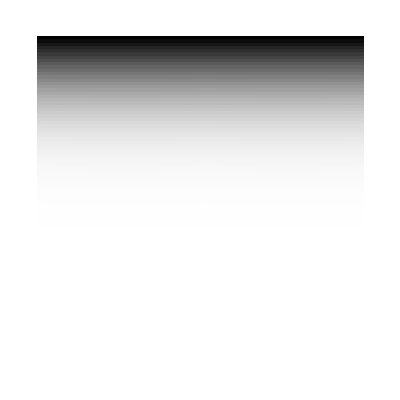

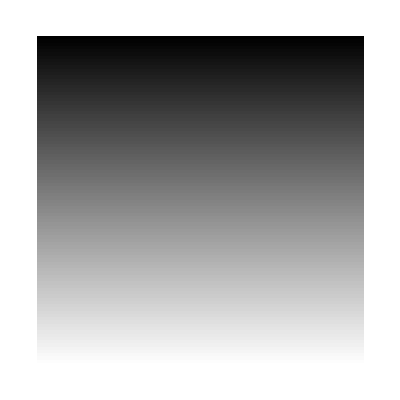

```mathematica
ArrayPlot[Import["gauss100_02.dat","Table"]]
ArrayPlot[Import["gauss100_03.dat","Table"]]
ArrayPlot[Import["gauss100_05.dat","Table"]]
```